```mathematica
Integrate[(Cosh[x]-1)/x,{x,0,I*t*u}]
```

-EulerGamma+CosIntegral[t u]-Log[t u]

```mathematica
FourierTransform[Log[t*u]/t^3,t,s]/.s->1
```

-1/2 ⅈ √(π/2) Log[u]

```mathematica
FourierTransform[1/t^3,t,s]/.s->1
```

-1/2 ⅈ √(π/2)

```mathematica
Integrate[Sin[t]/t^3 CosIntegral[t*u],t]
```

∫(CosIntegral[t u] Sin[t])/t^3 ⅆt

```mathematica
Limit[t*Sin[t]CosIntegral[t*u],t->0]
```

0

```mathematica
integrant=1/(2(a^2+μ^2))(μ*ArcTan[(2a*μ)/(μ^2+b^2-a^2)]-a/2 Log[((μ^2+b^2-a^2)^2+4 a^2 μ^2)/b^4])/.a->1/(√Subscript[ψ, 2])/.b->1//FunctionExpand//FullSimplify
```

(-Log[(1+μ^2)^2+1/ψ_2^2+(2 (-1+μ^2))/ψ_2] √ψ_2+2 μ ArcTan[(2 μ √ψ_2)/(-1+(1+μ^2) ψ_2)] ψ_2)/(4+4 μ^2 ψ_2)

```mathematica
integrant//Expand
```

-(Log[(1+μ^2)^2+1/ψ_2^2+(2 (-1+μ^2))/ψ_2] √ψ_2)/(4+4 μ^2 ψ_2)+(2 μ ArcTan[(2 μ √ψ_2)/(-1+(1+μ^2) ψ_2)] ψ_2)/(4+4 μ^2 ψ_2)

```mathematica
Integrate[%318[[1]],{μ,0,∞}]
```

$Aborted

```mathematica
Assuming[{Subscript[ψ, 2]>0,Element[μ,Reals],μ>0},Integrate[μ^2*integrant,μ]]//PowerExpand//Expand//FunctionExpand//Simplify
```

-1/(8 ψ_2)(2 ArcTan[(μ √ψ_2)/(1-√ψ_2)]+2 ArcTan[(μ √ψ_2)/(1+√ψ_2)]-2 ArcTan[μ √ψ_2] Log[(1+μ^2)^2+1/ψ_2^2+(2 (-1+μ^2))/ψ_2]-2 ArcTan[(μ √ψ_2)/(1-√ψ_2)] Log[μ-ⅈ/(√ψ_2)]-2 ArcTan[(μ √ψ_2)/(1+√ψ_2)] Log[μ-ⅈ/(√ψ_2)]-2 ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)]+2 ArcTan[μ √ψ_2] Log[-ⅈ+μ-ⅈ/(√ψ_2)]-2 ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)]+2 ArcTan[μ √ψ_2] Log[ⅈ+μ-ⅈ/(√ψ_2)]-2 ArcTan[(μ √ψ_2)/(1-√ψ_2)] Log[μ+ⅈ/(√ψ_2)]-2 ArcTan[(μ √ψ_2)/(1+√ψ_2)] Log[μ+ⅈ/(√ψ_2)]+2 ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)]+2 ArcTan[μ √ψ_2] Log[-ⅈ+μ+ⅈ/(√ψ_2)]+2 ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)]+2 ArcTan[μ √ψ_2] Log[ⅈ+μ+ⅈ/(√ψ_2)]+ⅈ Log[μ+ⅈ/(√ψ_2)] Log[1-ⅈ μ+1/(√ψ_2)]-ⅈ Log[μ-ⅈ/(√ψ_2)] Log[1+ⅈ μ+1/(√ψ_2)]+ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)] Log[-ⅈ (-2+√ψ_2)]-ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ (-2+√ψ_2)]+ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ (2+√ψ_2)]-ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ (2+√ψ_2)]-ⅈ Log[μ-ⅈ/(√ψ_2)] Log[2+√ψ_2]+ⅈ Log[μ+ⅈ/(√ψ_2)] Log[2+√ψ_2]+ⅈ Log[μ-ⅈ/(√ψ_2)] Log[1+(1-ⅈ μ) √ψ_2]-ⅈ Log[μ+ⅈ/(√ψ_2)] Log[1+(1+ⅈ μ) √ψ_2]+ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ-μ √ψ_2]+ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ-μ √ψ_2]+ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)] Log[-ⅈ+μ √ψ_2]+ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)] Log[-ⅈ+μ √ψ_2]-ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ+μ √ψ_2]-ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ+μ √ψ_2]-ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ+μ √ψ_2]-ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ+μ √ψ_2]+ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)] Log[-ⅈ √ψ_2]-ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ √ψ_2]-ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)] Log[ⅈ √ψ_2]+ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)] Log[ⅈ √ψ_2]+2 ArcTan[(μ √ψ_2)/(1-√ψ_2)] Log[1+μ^2 ψ_2]+2 ArcTan[(μ √ψ_2)/(1+√ψ_2)] Log[1+μ^2 ψ_2]+2 ArcTan[(2 μ √ψ_2)/(-1+(1+μ^2) ψ_2)] Log[1+μ^2 ψ_2]-ⅈ PolyLog[2,-ⅈ μ-1/(√ψ_2)]+ⅈ PolyLog[2,1-ⅈ μ-1/(√ψ_2)]+ⅈ PolyLog[2,ⅈ μ-1/(√ψ_2)]-ⅈ PolyLog[2,1+ⅈ μ-1/(√ψ_2)]-ⅈ PolyLog[2,1-ⅈ μ+1/(√ψ_2)]+ⅈ PolyLog[2,1+ⅈ μ+1/(√ψ_2)]-ⅈ PolyLog[2,(-1+(1-ⅈ μ) √ψ_2)/(-2+√ψ_2)]+ⅈ PolyLog[2,(1+(1-ⅈ μ) √ψ_2)/(2+√ψ_2)]+ⅈ PolyLog[2,(-1+(1+ⅈ μ) √ψ_2)/(-2+√ψ_2)]-ⅈ PolyLog[2,(1+(1+ⅈ μ) √ψ_2)/(2+√ψ_2)]-ⅈ PolyLog[2,(1-ⅈ μ √ψ_2)/(2+√ψ_2)]+ⅈ PolyLog[2,(1+ⅈ μ √ψ_2)/(2+√ψ_2)]-1/Abs[-1+√ψ_2]ⅈ (Log[-1+Abs[-1+√ψ_2]] Log[μ-ⅈ/(√ψ_2)]-Log[1+Abs[-1+√ψ_2]] Log[μ-ⅈ/(√ψ_2)]-Log[-1+Abs[-1+√ψ_2]] Log[μ+ⅈ/(√ψ_2)]+Log[1+Abs[-1+√ψ_2]] Log[μ+ⅈ/(√ψ_2)]+Log[μ-ⅈ/(√ψ_2)] Log[Abs[-1+√ψ_2]-ⅈ μ √ψ_2]+Log[μ+ⅈ/(√ψ_2)] Log[Abs[-1+√ψ_2]-ⅈ μ √ψ_2]-Log[μ-ⅈ/(√ψ_2)] Log[Abs[-1+√ψ_2]+ⅈ μ √ψ_2]-Log[μ+ⅈ/(√ψ_2)] Log[Abs[-1+√ψ_2]+ⅈ μ √ψ_2]-PolyLog[2,(-1-ⅈ μ √ψ_2)/(-1+Abs[-1+√ψ_2])]-PolyLog[2,(1-ⅈ μ √ψ_2)/(1+Abs[-1+√ψ_2])]+PolyLog[2,(-1+ⅈ μ √ψ_2)/(-1+Abs[-1+√ψ_2])]+PolyLog[2,(1+ⅈ μ √ψ_2)/(1+Abs[-1+√ψ_2])]) (-1+√ψ_2)+2 (-6 μ-2 ArcTan[(μ √ψ_2)/(1-√ψ_2)]+2 ArcTan[(μ √ψ_2)/(1+√ψ_2)]+μ Log[(1+μ^2)^2+1/ψ_2^2+(2 (-1+μ^2))/ψ_2]-ⅈ Log[-ⅈ+μ-ⅈ/(√ψ_2)]+ⅈ Log[ⅈ+μ-ⅈ/(√ψ_2)]-ⅈ Log[-ⅈ+μ+ⅈ/(√ψ_2)]+ⅈ Log[ⅈ+μ+ⅈ/(√ψ_2)]) √ψ_2+2 (ArcTan[(μ √ψ_2)/(1-√ψ_2)]+ArcTan[(μ √ψ_2)/(1+√ψ_2)]-μ^2 ArcTan[(2 μ √ψ_2)/(-1+(1+μ^2) ψ_2)]) ψ_2)

```mathematica
Limit[%55,μ->0]
```

ConditionalExpression[-1/(16 ψ_2)(ⅈ (2 Log[-ⅈ/(-ⅈ+√(-(1+√ψ_2)^2/ψ_2) √ψ_2)] Log[-√(-(1+√ψ_2)^2/ψ_2)]-2 Log[ⅈ/(ⅈ+√(-(1+√ψ_2)^2/ψ_2) √ψ_2)] Log[-√(-(1+√ψ_2)^2/ψ_2)]+Log[-ⅈ/(-ⅈ+√(-(-1+√ψ_2)^2/ψ_2) √ψ_2)] (2 Log[-√(-(-1+√ψ_2)^2/ψ_2)]-Log[-(-1+√ψ_2)^2/ψ_2])+Log[ⅈ/(ⅈ+√(-(-1+√ψ_2)^2/ψ_2) √ψ_2)] (-2 Log[-√(-(-1+√ψ_2)^2/ψ_2)]+Log[-(-1+√ψ_2)^2/ψ_2])-Log[-ⅈ/(-ⅈ+√(-(1+√ψ_2)^2/ψ_2) √ψ_2)] Log[-(1+√ψ_2)^2/ψ_2]+Log[ⅈ/(ⅈ+√(-(1+√ψ_2)^2/ψ_2) √ψ_2)] Log[-(1+√ψ_2)^2/ψ_2]-2 Log[1+1/(√ψ_2)] Log[-ⅈ/(√ψ_2)]+2 Log[(1+√ψ_2)/(2+√ψ_2)] Log[-ⅈ/(√ψ_2)]+2 Log[1+1/(√ψ_2)] Log[ⅈ/(√ψ_2)]-2 Log[(1+√ψ_2)/(2+√ψ_2)] Log[ⅈ/(√ψ_2)])+(Log[(1+Abs[-1+√ψ_2])/(-1+Abs[-1+√ψ_2])] (π+2 ⅈ Log[-ⅈ/(√ψ_2)]+ⅈ Log[ψ_2]) (-1+√ψ_2))/Abs[-1+√ψ_2]-2 ((2 Log[-√(-(-1+√ψ_2)^2/ψ_2)]-Log[-(-1+√ψ_2)^2/ψ_2]) √(-(-1+√ψ_2)^2/ψ_2)+2 Log[-√(-(1+√ψ_2)^2/ψ_2)] √(-(1+√ψ_2)^2/ψ_2)-Log[-(1+√ψ_2)^2/ψ_2] √(-(1+√ψ_2)^2/ψ_2)) √ψ_2), ]

```mathematica
%55[[3]][[4]]
```

2 ArcTan[μ √ψ_2] Log[μ+√(-(-1+√ψ_2)^2/ψ_2)]

```mathematica
Limit[%55[[3]][[3]],μ->+∞]
```

∞

```mathematica
Assuming[{Subscript[ψ, 2]>0,Re[μ]>0,Element[μ,Reals]},Integrate[μ^2*integrant,{μ,0,+∞},PrincipalValue->True]]
```

$Aborted

```mathematica
Chi[u_]:=Integrate[(Cosh[x]-1)/x,{x,0,u}]
```

```mathematica
NIntegrate[CoshIntegral[I*t*200]/t^3 Exp[I*t],{t,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.99964}. NIntegrate obtained 1.09264-0.0567595 ⅈ and 0.704089 for the integral and error estimates.

1.09264-0.0567595 ⅈ

```mathematica
Residue[(CosIntegral[t]Exp[I*t])/t^3,{t,0}]
```

Residue[(ⅇ^(ⅈ t) CosIntegral[t])/t^3,{t,0}]

```mathematica
CosIntegral[0]
```

-∞

```mathematica
Assuming[{Element[u,Reals],u>0},Series[(ⅇ^(ⅈ t) CosIntegral[t*u])/t^3,{t,0,3}]]
```

(EulerGamma+Log[t]+Log[u])/t^3+(ⅈ (EulerGamma+Log[t]+Log[u]))/t^2+(-2 EulerGamma-u^2-2 Log[t]-2 Log[u])/(4 t)-1/12 ⅈ (2 EulerGamma+3 u^2+2 Log[t]+2 Log[u])+1/96 (4 EulerGamma+12 u^2+u^4+4 Log[t]+4 Log[u]) t+1/480 ⅈ (4 EulerGamma+20 u^2+5 u^4+4 Log[t]+4 Log[u]) t^2+((-12 EulerGamma-90 u^2-45 u^4-2 u^6-12 Log[t]-12 Log[u]) t^3)/8640+O[t]^4

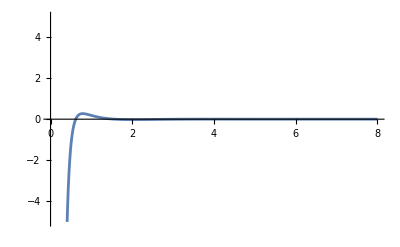

```mathematica
Plot[CosIntegral[t]/t^3*Cos[t],{t,0,8},PlotRange->{-5,5}]
```

```mathematica
Limit[CosIntegral[t]/t^3*Sin[t],t->1]
```

CosIntegral[1] Sin[1]

```mathematica
Clear[func];
func[t_]:=CosIntegral[t*u]/t^3*Sin[t]
```

```mathematica
Limit[t^3*func[t],t->0]
```

0

```mathematica
Clear[res]
res[n_]:=1/Factorial[(n-1)]*Limit[D[t^n func[t],{t,n-1}],t->0]
```

```mathematica
res[4]
```

Indeterminate

```mathematica
Limit[CosIntegral[t*u]/t^3,t->+∞]
```

ConditionalExpression[0, u>0]

```mathematica
Residue[CosIntegral[t]/t^3*Cos[u*t],{t,0}]
```

Residue[(Cos[t u] CosIntegral[t])/t^3,{t,0}]

```mathematica
Series[CosIntegral[t]/t^3*Exp[u*t],{t,0,3}]
```

(EulerGamma+Log[t])/t^3+(u (EulerGamma+Log[t]))/t^2+(-1+2 EulerGamma u^2+2 u^2 Log[t])/(4 t)+1/12 (-3 u+2 EulerGamma u^3+2 u^3 Log[t])+1/96 (1-12 u^2+4 EulerGamma u^4+4 u^4 Log[t]) t+1/480 (5 u-20 u^3+4 EulerGamma u^5+4 u^5 Log[t]) t^2+((-2+45 u^2-90 u^4+12 EulerGamma u^6+12 u^6 Log[t]) t^3)/8640+O[t]^4

```mathematica
Series[CosIntegral[t]/t^3*Exp[u*t],{t,0,3}]//Normal//PowerExpand
```

(EulerGamma+Log[t])/t^3+(u (EulerGamma+Log[t]))/t^2+(-1+2 EulerGamma u^2+2 u^2 Log[t])/(4 t)+1/12 (-3 u+2 EulerGamma u^3+2 u^3 Log[t])+1/96 t (1-12 u^2+4 EulerGamma u^4+4 u^4 Log[t])+1/480 t^2 (5 u-20 u^3+4 EulerGamma u^5+4 u^5 Log[t])+(t^3 (-2+45 u^2-90 u^4+12 EulerGamma u^6+12 u^6 Log[t]))/8640

```mathematica
CosIntegral[-x]//FunctionExpand
```

CosIntegral[x]+Log[-x]-Log[x]

```mathematica
CosIntegral[t]*Exp[u*t]/.t->0
```

-∞

```mathematica
Series[Exp[I*t],{t,0,6}]
```

1+ⅈ t-t^2/2-(ⅈ t^3)/6+t^4/24+(ⅈ t^5)/120-t^6/720+O[t]^7

```mathematica
NIntegrate[Exp[I*t]/t^3 CosIntegral[2*t],{t,-∞,-10^-10}]+NIntegrate[Exp[I*t]/t^3 CosIntegral[2*t],{t,10^-10,∞}]
```

-3.14153×10^10-1.5708×10^20 ⅈ

```mathematica
Pi/(4*2^2)(4-2^2-(2^2+4)BesselJ[0,2]+2*2*BesselJ[1,2])//N
```

0.101272

```mathematica
NIntegrate[Exp[I*t] CosIntegral[2*t]/t^3,{t,0.00000000001,∞}]+NIntegrate[Exp[I*t] CosIntegral[2*t]/t^3,{t,-∞,-0.00000000001}]
```

-3.14153×10^11-1.5708×10^22 ⅈ

```mathematica
Series[Integrate[(1-Cos[x])/x,{x,0,u}],{u,0,0}]
```

O[u]^2

```mathematica
cin[x_]:=Integrate[(1-Cos[ω])/ω,{ω,0,x}]
```

```mathematica
Residue[cin[u*t]*Exp[I*t]/t^3,{t,0}]
```

Residue[(ⅇ^(ⅈ t) (EulerGamma-CosIntegral[t u]+Log[t u]))/t^3,{t,0}]

```mathematica
FourierTransform[ExpIntegralE[1,I*t],t,s]
```

FourierTransform[ExpIntegralE[1,ⅈ t],t,s]

```mathematica
Limit[1/(t^3-I*ϵ)CosIntegral[t],t->+∞]
```

0

```mathematica
Limit[CosIntegral[t],t->+∞]
```

0

```mathematica
Solve[t^3==I*ϵ,t]
```

{{t→-ⅈ ϵ^(1/3)},{t→(-1)^(1/6) ϵ^(1/3)},{t→(-1)^(5/6) ϵ^(1/3)}}

```mathematica
RealValuedNumberQ[(-1)^(5/6)]
```

False

```mathematica
Im[(-1)^(1/6)]
```

1/2

```mathematica
Residue[Exp[I*u*t]/(t^3-I*ϵ)CosIntegral[t],{t,(-1)^(1/6) ϵ^(1/3)}]+Residue[Exp[I*u*t]/(t^3-I*ϵ)CosIntegral[t],{t,(-1)^(5/6) ϵ^(1/3)}]
```

-((-1)^(2/3) ⅇ^((-1)^(2/3) u ϵ^(1/3)) CosIntegral[(-1)^(1/6) ϵ^(1/3)])/(3 ϵ^(2/3))+((-1)^(1/3) ⅇ^(-(-1)^(1/3) u ϵ^(1/3)) CosIntegral[(-1)^(5/6) ϵ^(1/3)])/(3 ϵ^(2/3))

```mathematica
Limit[%406,ϵ->0]
```

Indeterminate